```mathematica
u== x+√y;
Manipulate[Plot[{(c-x)^2,(c+1-x)^2,(c+2-x)^2,(c+3-x)^2},{x,0,20}],{c,0,10}]
```

```mathematica
D[(c-x)^2,x]
```

-2 (c-x)

```mathematica
D[ x+√y,x]
D[ x+√y,y]
```

1

1/(2 √y)

```mathematica
Simplify[1/(1/(2 √y))]
```

```mathematica
2 √y== p/k
y== (p/(k*2))^2
```

```mathematica
p*x+k*y==w
```

```mathematica
Simplify[Solve[p*x+k*(p/(k*2))^2==w ,x]]
```

{{x→-p/(4 k)+w/p}}

```mathematica
Solve[p*(-p^2+4 k w)/(4 k p)+k*y==w ,y]
```

```mathematica
{{y->p^2/(4 k^2)}}

Plot[{Log[(80-Sqrt[2*Exp[a]])^2/2], Log[40]+Log[80]},{a,0,8.08}]
```

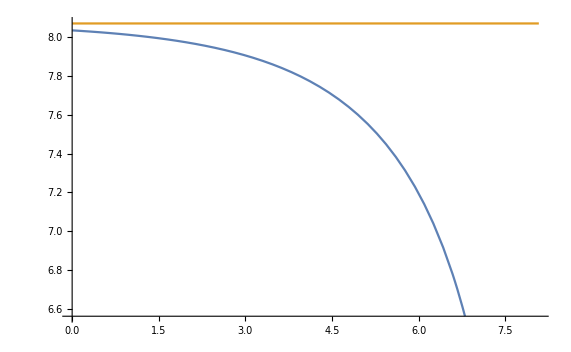

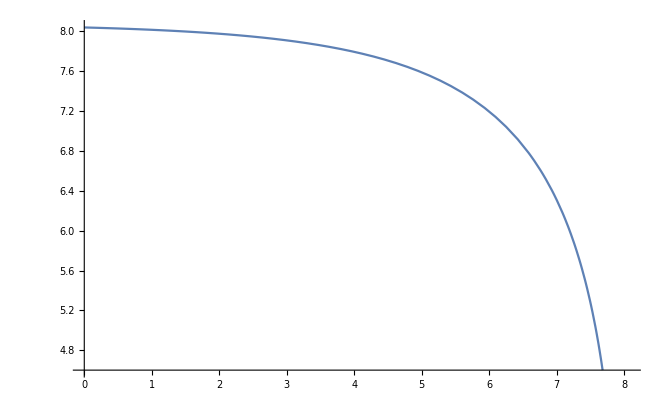

```mathematica
}
```

```mathematica
Plot[{Log[(80-Sqrt[2*Exp[a]])^2/2], Log[40]+Log[80]},{a,0,9},{y,0,10}]
```

Plot::nonopt: Options expected (instead of {y,0,10}) beyond position 2 in Plot[{Log[1/2 (80-√(«1»))^2],Log[40]+Log[80]},{a,0,9},{y,0,10}]. An option must be a rule or a list of rules.

Plot[{Log[1/2 (80-√(2 Exp[a]))^2],Log[40]+Log[80]},{a,0,9},{y,0,10}]

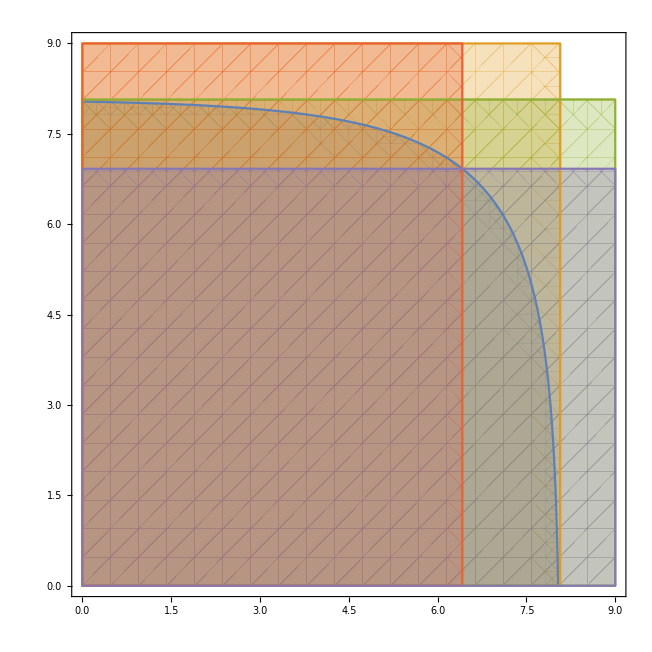

```mathematica
RegionPlot[{Sqrt[2*Exp[x]]+Sqrt[2*Exp[y]]<80,x<Log[40]+Log[80],y<Log[40]+Log[80],x<Log[35]+Log[17.5],y<Log[45]+Log[22.5]},{x,0,9},{y,0,9}]
```

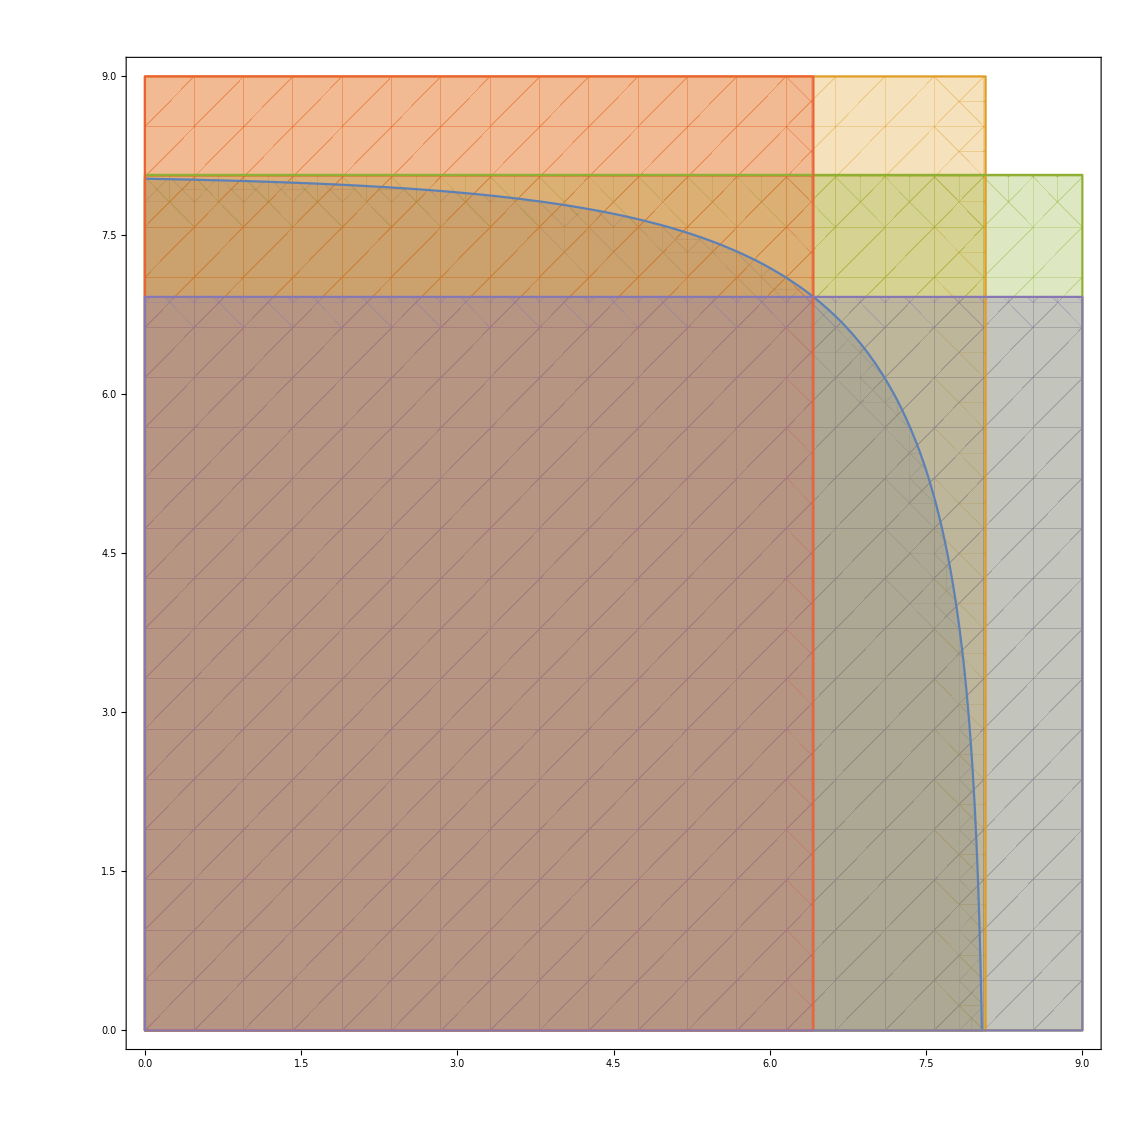

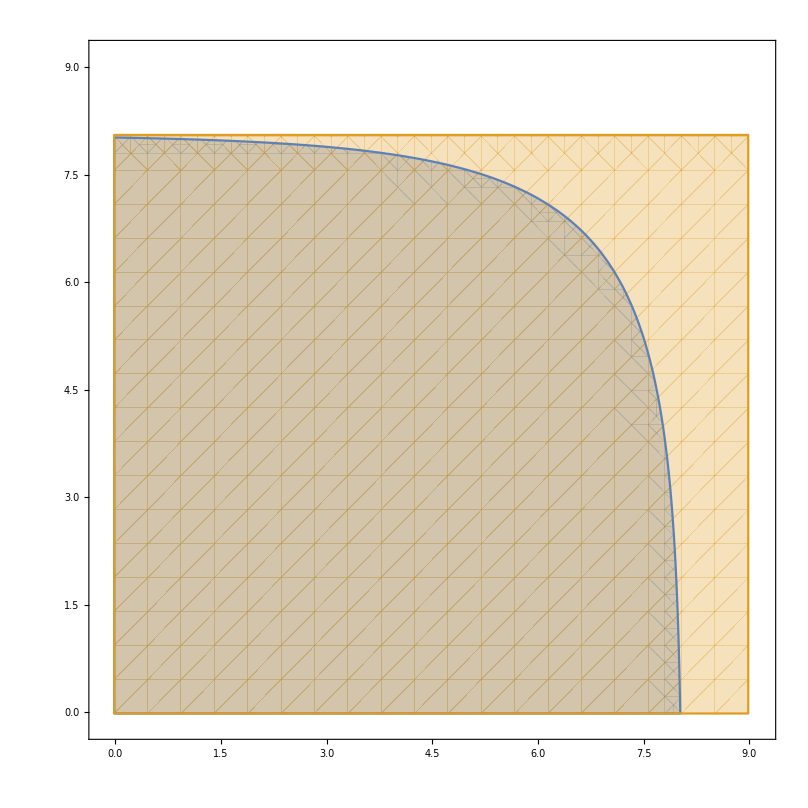

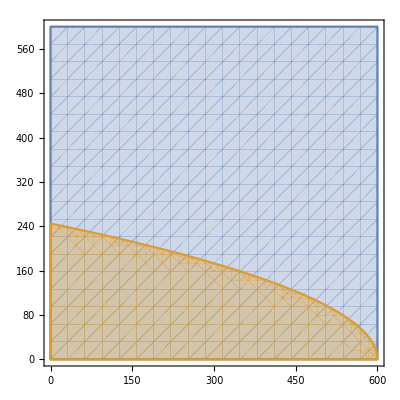

```mathematica
RegionPlot[{Log[x]+0.9Log[y]<2*Log[600],y<10*Sqrt[600-x]},{x,0,600},{y,0,600}]
```

```mathematica
Manipulate[Plot[Exp[(u-Log[x])*10/0.9],{x,0,600}],{u,0,2*Log[600]}]
```

```mathematica
Manipulate[Plot[Log[x]+0.9Log[y],{x,0,600}],{y,0,10*Sqrt[600-x]}]
```

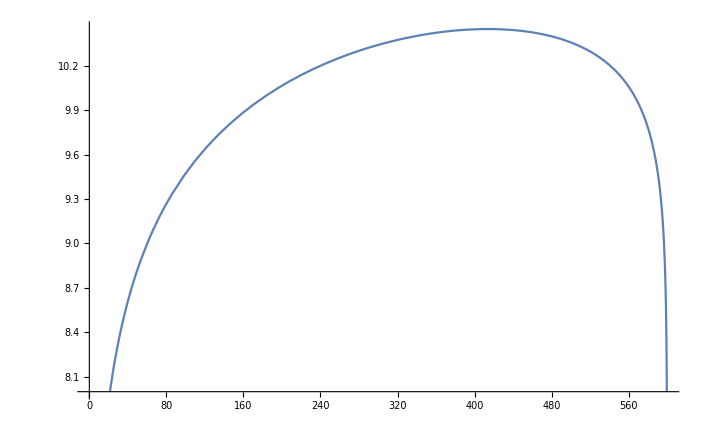

```mathematica
Plot[Log[x]+0.9Log[10*Sqrt[600-x]],{x,0,600}]
```